# Playing with precomputed g values

In the other file, we compute g values and append them to the file “computedG.csv”. In this file, we import the data from this file just to look at it. Recall that for the computation, we store polynomials as arrays; that is, a+bk+ck^3 == {a,b,0,c}. For viewing purposes, in this file, we convert them back to polynomials in k.

```mathematica
Remove["Global`*"];
```

```mathematica
gFilename="/Users/jtiosue/Documents/Repositories/LXEB/Mathematica/computedG.csv";
```

```mathematica
g=Association@@Table[
tup[[1]]->∑_(i=0)^(Length[tup[[2]]]-1) tup[[2]][[i+1]] k^i,
{tup,ToExpression@Import@gFilename}
];
```

### How many have we computed so far?

```mathematica
g//Length
```

1331

### Print all of the a={0,0,0} entries

```mathematica
ns=Select[Keys@g,#[[2]]=={0,0,0}&][[All,1]]//Sort;
```

```mathematica
Table[
{n,g[{n,{0,0,0}}]},
{n,ns}
]//TableForm
```

1 | 2 k+2 k^2
2 | 176 k+184 k^2+64 k^3+8 k^4
3 | 74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
4 | 90408960 k+121065984 k^2+63951360 k^3+17759616 k^4+2872320 k^5+278016 k^6+15360 k^7+384 k^8
5 | 237617971200 k+343673303040 k^2+202717824000 k^3+65407180800 k^4+12943123200 k^5+1655781120 k^6+139392000 k^7+7603200 k^8+249600 k^9+3840 k^10
6 | 1159859699712000 k+1780791422976000 k^2+1140813555425280 k^3+410191172628480 k^4+93270554265600 k^5+14247651916800 k^6+1508640215040 k^7+112075453440 k^8+5807462400 k^9+203443200 k^10+4423680 k^11+46080 k^12
7 | 9462639862480896000 k+15246273259929600000 k^2+10421808429874544640 k^3+4071608172016680960 k^4+1026952754189967360 k^5+178307659157483520 k^6+22109565749483520 k^7+1998175940167680 k^8+132745496647680 k^9+6466813839360 k^10+227377059840 k^11+5549967360 k^12+85800960 k^13+645120 k^14
8 | 119720630833266032640000 k+200796561000272756736000 k^2+144711123926956218777600 k^3+60415241009583386787840 k^4+16528349328270038138880 k^5+3166169317852953968640 k^6+441843922442755768320 k^7+46026366788113367040 k^8+3629790873271664640 k^9+218065033148497920 k^10+9969100754780160 k^11+343607014195200 k^12+8742088212480 k^13+157223485440 k^14+1816657920 k^15+10321920 k^16
9 | 2221247018056830041456640000 k+3855175197947055480766464000 k^2+2904237338727171996883353600 k^3+1280729580277534827070095360 k^4+374303224008993996354355200 k^5+77564194739580892836003840 k^6+11877470107076545413120000 k^7+1380287720700295139819520 k^8+123832881173454682521600 k^9+8665188337608815738880 k^10+475146042332361523200 k^11+20406933381977210880 k^12+682378385994547200 k^13+17534066558238720 k^14+337908282163200 k^15+4664186634240 k^16+41803776000 k^17+185794560 k^18
10 | 57875363345940374711225548800000 k+103476098681327348341580759040000 k^2+80965230375737197759140200448000 k^3+37396163878121465462090052403200 k^4+11549033918313096837275320320000 k^5+2553455926152348117269741568000 k^6+421694240195528846498856960000 k^7+53496251894559728028037939200 k^8+5312875561161631329484800000 k^9+418297517171370849632256000 k^10+26311610109360809705472000 k^11+1327075152807942468403200 k^12+53660329481243197440000 k^13+1732280071673217024000 k^14+44252111014723584000 k^15+880831333741363200 k^16+13306420592640000 k^17+145421402112000 k^18+1040449536000 k^19+3715891200 k^20
11 | 2045846254375871026944282722304000000 k+3754756022542427749718469220761600000 k^2+3036540816683854203446772734361600000 k^3+1459584741451196867679383099277312000 k^4+472477053335440502937507615630950400 k^5+110338850085947626637087851570790400 k^6+19408962083693217370343998488576000 k^7+2647105238020097389884208054272000 k^8+285604538987756004915330573926400 k^9+24722331120708172694587205222400 k^10+1733426526911822577735892992000 k^11+99042015520504682810376192000 k^12+4624794687268006821848678400 k^13+176490204956714899301990400 k^14+5487825810170990297088000 k^15+138150937332359626752000 k^16+2785665572983170662400 k^17+44232479114290790400 k^18+537960233631744000 k^19+4770498281472000 k^20+27876615782400 k^21+81749606400 k^22
12 | 95391755978551627984315810937044992000000 k+179204566298221128108188538543852748800000 k^2+149211417132572995348096252025556172800000 k^3+74269070732332919813012637280565723136000 k^4+25043132500802798445487604296060187443200 k^5+6130332032327408168402186331644284108800 k^6+1137970861000694185537909022671031500800 k^7+164994391466771392603106045989591449600 k^8+19079536338562466167577024543273779200 k^9+1786298200347404901271609828756684800 k^10+136870721872567023351054350470348800 k^11+8647530520047195308963658832281600 k^12+452660108928649181781340402483200 k^13+19677990448219037704559316172800 k^14+710489959309228528850750668800 k^15+21258602346398524390873497600 k^16+524601391220488492233523200 k^17+10593145227495451970764800 k^18+172953716869355588812800 k^19+2242267733870877081600 k^20+22429460312830771200 k^21+164626703371468800 k^22+800492145868800 k^23+1961990553600 k^24
13 | 5731225923923558774941392274715364556800000000 k+10995285392857893153955248685346237448192000000 k^2+9396291655808965095857136949412775120076800000 k^3+4823815933413165634688518642221969309696000000 k^4+1686045017910136620172834418161358173372416000 k^5+430058190086748619438675818711864313066291200 k^6+83645952925319049329502297583443614525030400 k^7+12783496470888327284800570983293708874547200 k^8+1568365356359712581337663330310042524057600 k^9+156911530060590982522321872019058904268800 k^10+12951188717221020170081063931182736998400 k^11+889402203491379787392669332937061171200 k^12+51123876481473485233393645287741849600 k^13+2469279906078287574326646394375372800 k^14+100414246857345028777569369351782400 k^15+3438485145193302858001225560883200 k^16+98981123012613172252367231385600 k^17+2386435230358072393509686476800 k^18+47901928622817660568495718400 k^19+793419435675853983527731200 k^20+10705955428609057986969600 k^21+115483486268174421196800 k^22+966895361054893670400 k^23+5971027875279667200 k^24+24536653863321600 k^25+51011754393600 k^26
14 | 435016381900506856831866584394857505557053440000000 k+850641028100102107599405928590873158561562624000000 k^2+744177677930000410594651099246438476934230835200000 k^3+392765934940263200309086966908864137645072056320000 k^4+141740164249577464900211506111838387825591451648000 k^5+37493148697132609766465931507814730382168607948800 k^6+7597851558902861415701751133564594587074297856000 k^7+1215825186432182467595066663143504988364550963200 k^8+157024523449803421413981166889468636090597376000 k^9+16634253576618990270219734078166208622886912000 k^10+1463069617573437699170674414460307121373184000 k^11+107829884801953134624830915120306552045568000 k^12+6704872949713068320442207470552881299456000 k^13+353460585217411756368615210273120190464000 k^14+15848270560956045928785182794306289664000 k^15+605395215484940758719723060011728896000 k^16+19706010712997242975338011239120896000 k^17+545882883444642686423346916098048000 k^18+12831768021906489769491739705344000 k^19+254754412321883136950714499072000 k^20+4242568218864654435112452096000 k^21+58698815345837682060165120000 k^22+665683785032527043887104000 k^23+6068550264995614556160000 k^24+43153979244206358528000 k^25+227331434890867507200 k^26+799864308891648000 k^27+1428329123020800 k^28
15 | 41015423552674622914217007993321376654552989696000000000 k+81613496237916814279430189403710232698076769812480000000 k^2+72935761736795099434027426505273001970382596472832000000 k^3+39469167746786016789673464713765044161807115301683200000 k^4+14658489647149365369688134226458018866014452417822720000 k^5+4005642374982347571306303006413308386663757705641984000 k^6+841894008369147689651597769986278088816180015923200000 k^7+140314899731321919218954100732589805676646147031040000 k^8+18958724346586671613395879609136034078693177425920000 k^9+2111287213433663243286190556005935537597978771456000 k^10+196239008525105625054941044900553187120906240000000 k^11+15371809678935519387240534148764753205395456000000 k^12+1022320603718009549911127670751367330896281600000 k^13+58049535178022196007860213139681051630632960000 k^14+2825641405486138851904157325371731083264000000 k^15+118224870574226811803586692429170448793600000 k^16+4257915065406086597360800798054809600000000 k^17+132032020524898697644647263211796561920000 k^18+3521455664436908154050817819672576000000 k^19+80598885646750705233704706165964800000 k^20+1577163950259190692632000357990400000 k^21+26242986144319150133970374492160000 k^22+368545153781264680341209088000000 k^23+4324073226748208292770611200000 k^24+41797618501349598434426880000 k^25+326291846083558187728896000 k^26+1995254019802320076800000 k^27+9071961008410460160000 k^28+27638168530452480000 k^29+42849873690624000 k^30

## Run our various tests on the values

### Check n=3, a = {0,0,0}

```mathematica
g[{3,{0,0,0}}]==74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
```

True

### Check that the sum of the coefficients is equal to the number of graphs

```mathematica
graphCounter[n_,a_]:=With[{a12=a[[1]],a13=a[[2]],a23=a[[3]]},
Binomial[2 n,a12] Binomial[2 n-a12,a13]*Binomial[2 n,a12] Binomial[2 n-a12,a23]*Binomial[2 n,a13] Binomial[2 n-a13,a23]*a12!*a13!*a23!*(2 n-a12-a13-1)!!*(2 n-a12-a23-1)!!*(2 n-a13-a23-1)!!*4^n
];
```

```mathematica
Table[
(g[key]/.k->1)==graphCounter@@key,
{key,Keys@g}
]//AllTrue[#&]
```

True

### Check the coefficient of the highest degree

```mathematica
(*coef[n_]:=(2n-1)!!+∑_(i=1)^n (2i-1)!!(2n-2i-1)!!Binomial[n,i];*)
coef[n_]=(2n)!!;
```

```mathematica
Table[
CoefficientList[g[{n,{0,0,0}}],k][[-1]]==coef@n,
{n,ns}
]//AllTrue[#&]
```

True

### Check that the number of a for a given n is less than roughly n^3

```mathematica
counting=ConstantArray[0,Length@ns];
Do[
counting[[key[[1]]]]+=1;,
{key,Keys@g}
];
```

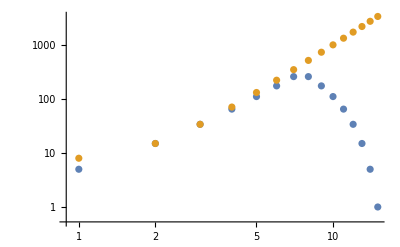

```mathematica
ListLogLogPlot@{counting,ns^3+7}
```

```mathematica
hafnian[n_]:=(2n-1)!!g[{n,{0,0,0}}];
```

## Plot coefficients of k

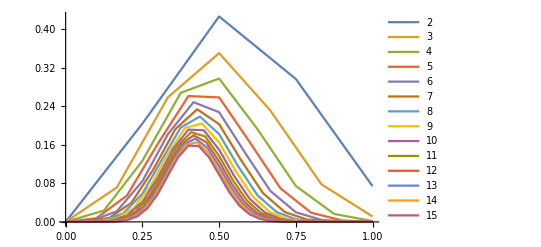

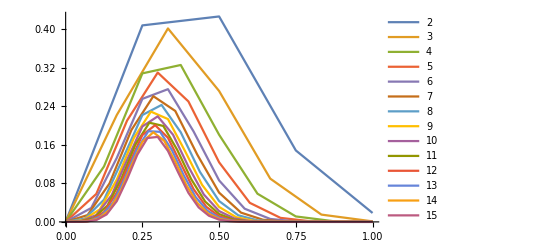

```mathematica
l[n_]:=CoefficientList[g[{n,{0,0,0}}],k];
t[n_,kk_]:=With[{ll=l@n,tot=g[{n,{0,0,0}}]/.k->kk@n},
Table[{(i-1)/(Length@ll-1),ll[[i]](kk@n)^(i-1)/tot},{i,Length@ll}]
];
plot[nns_,kk_]:=ListPlot[Table[t[n,kk],{n,nns}],PlotLegends->nns,Joined->True,PlotRange->All];
plot[Drop[ns,1],#&] (* k = n *)
plot[Drop[ns,1],#/2&] (* k = n/2 *)
```